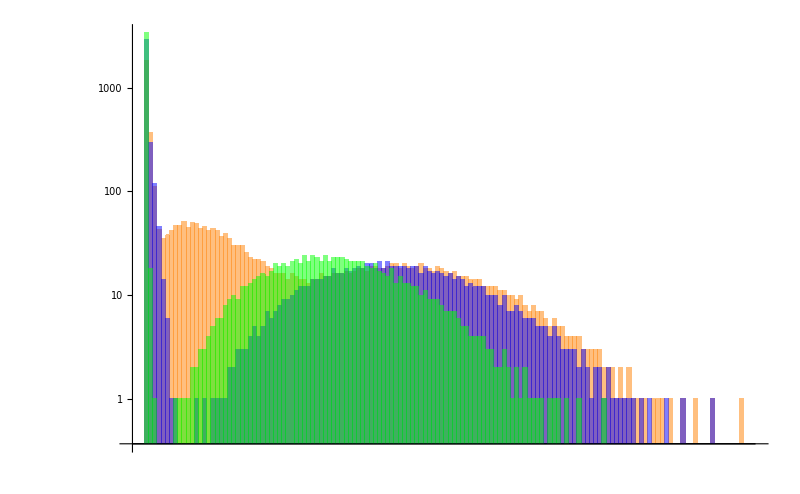

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[BarChart,BaseStyle->{FontSize->18}];
data1 = Import[y<>"/averageResults/data2-0.01-100-true-turtles.csv"];
data2 = Import[y<>"/averageResults/data2-0.001-100-true-turtles.csv"];
data3 = Import[y<>"/averageResults/data2-1.0E-4-100-true-turtles.csv"];
Fdata1 = Flatten[data1];
Fdata2 = Flatten[data2];
Fdata3 = Flatten[data3];

plot=Legended[Show[{{BarChart[{Fdata1},ImageSize->800,  ChartStyle->{Directive[Orange,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"], BarChart[{Fdata2},ImageSize->800, ChartStyle->{Directive[Blue,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"], BarChart[{Fdata3},ImageSize->800, ChartStyle->{Directive[Green,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"]}}, Frame->{{True, None},{True, None}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{50,"50"},{100,"100"}, {144,"144"}},None}}, FrameLabel->{"Publicaciones","Número de grupos de investigación"}, FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}], Placed[SwatchLegend[{Directive[Orange,Opacity[.5]],Directive[Blue,Opacity[.5]],Directive[Green,Opacity[.5]]},{Style["I1",17],Style["I2",17],Style["I3",17]},LegendMargins->{{35,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.8,0.5},{0,0}}]];
Export["DistribucionProductividadCompetencia.png",plot];

Show[BarChart[{Fdata1},ImageSize->800,  ChartStyle->{Directive[Orange,Opacity[.5]]}, ScalingFunctions->"Log"],BarChart[{Fdata2},ImageSize->800, ChartStyle->{Directive[Blue,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"],BarChart[{Fdata3},ImageSize->800, ChartStyle->{Directive[Green,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"],FrameLabel->{{"Publicaciones"},{"Numero de Universidades"}}]
```